# Definitions

```mathematica
pSMC[t_,ρ_]:=(1+2ρ t)Exp[-t(1+ ρ t)]
```

```mathematica
pSMCP[t_,ρ_]:=(1+2ρ (1-Exp[-t]))Exp[-t+ 2ρ(1-t-Exp[-t])]
```

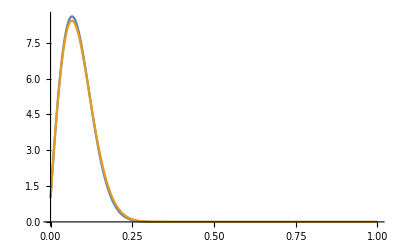

```mathematica
Module[{ρ=100},Plot[{pSMC[t,ρ],pSMCP[t,ρ]},{t,0,1},PlotRange->{All,{0,All}}]]
```

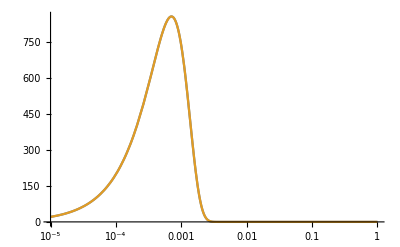

```mathematica
Module[{ρ=10^6},LogLinearPlot[{pSMC[t,ρ],pSMCP[t,ρ]},{t,0.01/√ρ,1},PlotRange->All]]
```

# Probability that the segments are identical

Prob(ID) = LT{p(T)}(2μ)

```mathematica
LaplaceTransform[pSMC[t,ρ],t,μ]
```

(ⅇ^((1+μ)^2/(4 ρ)) √π Erfc[(1+μ)/(2 √ρ)])/(2 √ρ)+(2 √ρ-ⅇ^((1+μ)^2/(4 ρ)) √π Erfc[(1+μ)/(2 √ρ)]-ⅇ^((1+μ)^2/(4 ρ)) √π μ Erfc[(1+μ)/(2 √ρ)])/(2 √ρ)

```mathematica
LaplaceTransform[pSMCP[t,ρ],t,μ]
```

2^(-1-μ-2 ρ) ⅇ^(2 ρ) ρ^(-1-μ-2 ρ) (Gamma[1+μ+2 ρ]-Gamma[1+μ+2 ρ,2 ρ])+2^(-μ-2 ρ) ⅇ^(2 ρ) ρ^(-μ-2 ρ) (Gamma[1+μ+2 ρ]-Gamma[1+μ+2 ρ,2 ρ])-2^(-1-μ-2 ρ) ⅇ^(2 ρ) ρ^(-1-μ-2 ρ) (Gamma[2+μ+2 ρ]-Gamma[2+μ+2 ρ,2 ρ])

# Moments

## Zeroth (check normalization)

```mathematica
Integrate[pSMC[t,ρ],{t,0,∞},Assumptions->ρ>0]
```

1

```mathematica
Integrate[pSMCP[t,ρ],{t,0,∞},Assumptions->ρ>0]
```

1

## Doing it exactly first

## Mean

```mathematica
Integrate[t pSMC[t,ρ],{t,0,∞},Assumptions->ρ>0]
```

(ⅇ^(1/4/ρ) √π Erfc[1/(2 √ρ)])/(2 √ρ)

```mathematica
smcMean[ρ_]:=(ⅇ^(1/4/ρ) √π Erfc[1/(2 √ρ)])/(2 √ρ);
```

```mathematica
Series[smcMean[ρ],{ρ,∞,1}]
```

1/2 √π √(1/ρ)-1/(2 ρ)+O[1/ρ]^(3/2)

This goes to √(π/ρ)/2 for large ρ.

```mathematica
Integrate[t pSMCP[t,ρ],{t,0,∞},Assumptions->ρ>0]
```

(ⅇ/2)^(2 ρ) ρ^(-2 ρ) (Gamma[2 ρ]+MeijerG[{{},{0,0}},{{-1,-1,2 ρ},{}},2 ρ]-MeijerG[{{},{0,0}},{{-1,-1,1+2 ρ},{}},2 ρ]+MeijerG[{{},{1,1}},{{0,0,1+2 ρ},{}},2 ρ])

```mathematica
smcpMean[ρ_]:=(ⅇ/2)^(2 ρ) ρ^(-2 ρ) (Gamma[2 ρ]+MeijerG[{{},{0,0}},{{-1,-1,2 ρ},{}},2 ρ]-MeijerG[{{},{0,0}},{{-1,-1,1+2 ρ},{}},2 ρ]+MeijerG[{{},{1,1}},{{0,0,1+2 ρ},{}},2 ρ]);
```

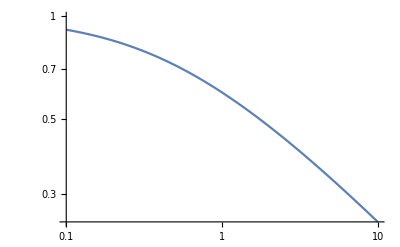

```mathematica
LogLogPlot[smcpMean[ρ],{ρ,0.1,10}]
```

```mathematica
Series[smcpMean[ρ],{ρ,∞,1}]
```

√π √(1/ρ)+O[1/ρ]^(3/2)

Different by a factor of 2 from SMC?

## Variance

```mathematica
Integrate[(t-smcMean[ρ])^2 pSMC[t,ρ],{t,0,∞},Assumptions->ρ>0]
```

-(-4+(2 ⅇ^(1/4/ρ) √π Erfc[1/(2 √ρ)])/(√ρ)+ⅇ^(1/2/ρ) π Erfc[1/(2 √ρ)]^2)/(4 ρ)

This goes to (1-π/4)/ρ  for large ρ.

For the SMC’, first just find the second moment:

```mathematica
Integrate[t^2 pSMCP[t,ρ],{t,0,∞},Assumptions->ρ>0]
```

1/(1+2 ρ)(ⅇ/2)^(2 ρ) ρ^(-1-2 ρ) (Gamma[1+2 ρ] Log[2]+ρ Gamma[1+2 ρ] Log[4]+Gamma[1+2 ρ] Log[ρ]+2 ρ Gamma[1+2 ρ] Log[ρ]+MeijerG[{{},{1,1,1}},{{0,0,0,2 (1+ρ)},{}},2 ρ]-MeijerG[{{},{1,1,1}},{{0,0,0,1+2 ρ},{}},2 ρ]-2 MeijerG[{{},{2,2,2}},{{1,1,1,2 (1+ρ)},{}},2 ρ]+MeijerG[{{},{2,2,2}},{{1,1,1,3+2 ρ},{}},2 ρ]-MeijerG[{{},{3,3,3}},{{2,2,2,3+2 ρ},{}},2 ρ]-Gamma[1+2 ρ] PolyGamma[0,1+2 ρ]-2 ρ Gamma[1+2 ρ] PolyGamma[0,1+2 ρ])

```mathematica
smcpMom2[ρ_]:=1/(1+2 ρ)(ⅇ/2)^(2 ρ) ρ^(-1-2 ρ) (Gamma[1+2 ρ] Log[2]+ρ Gamma[1+2 ρ] Log[4]+Gamma[1+2 ρ] Log[ρ]+2 ρ Gamma[1+2 ρ] Log[ρ]+MeijerG[{{},{1,1,1}},{{0,0,0,2 (1+ρ)},{}},2 ρ]-MeijerG[{{},{1,1,1}},{{0,0,0,1+2 ρ},{}},2 ρ]-2 MeijerG[{{},{2,2,2}},{{1,1,1,2 (1+ρ)},{}},2 ρ]+MeijerG[{{},{2,2,2}},{{1,1,1,3+2 ρ},{}},2 ρ]-MeijerG[{{},{3,3,3}},{{2,2,2,3+2 ρ},{}},2 ρ]-Gamma[1+2 ρ] PolyGamma[0,1+2 ρ]-2 ρ Gamma[1+2 ρ] PolyGamma[0,1+2 ρ]);
```

```mathematica
Series[smcpMom2[ρ]-smcpMean[ρ]^2,{ρ,∞,1}]
```

-π/ρ+O[1/ρ]^(3/2)

What, negative?!

Try calculating the variance directly:

```mathematica
Integrate[(t-smcpMean[ρ])^2 pSMCP[t,ρ],{t,0,∞},Assumptions->ρ>0]
```

((ⅇ/2)^(2 ρ) ρ^(-2 ρ) Gamma[2 ρ])/(1+2 ρ)+(ⅇ/2)^(6 ρ) ρ^(-6 ρ) Gamma[2 ρ]^3-(ⅇ/2)^(4 ρ) ρ^(-1-4 ρ) Gamma[2 ρ] Gamma[1+2 ρ]+(ⅇ/2)^(6 ρ) ρ^(-6 ρ) Gamma[2 ρ]^2 Gamma[1+2 ρ]-2^(-1-6 ρ) ⅇ^(6 ρ) ρ^(-1-6 ρ) Gamma[2 ρ]^2 Gamma[2+2 ρ]-2^(-1-6 ρ) ⅇ^(6 ρ) ρ^(-1-6 ρ) Gamma[2 ρ]^2 Gamma[1+2 ρ,2 ρ]-(ⅇ/2)^(6 ρ) ρ^(-6 ρ) Gamma[2 ρ]^2 Gamma[1+2 ρ,2 ρ]+2^(-1-6 ρ) ⅇ^(6 ρ) ρ^(-1-6 ρ) Gamma[2 ρ]^2 Gamma[2+2 ρ,2 ρ]+4^-ρ ⅇ^(2 ρ) ρ^(-1-2 ρ) Gamma[1+2 ρ] Log[2]-16^-ρ ⅇ^(4 ρ) ρ^(-1-4 ρ) Gamma[2 ρ] Gamma[1+2 ρ] Log[2]-16^-ρ ⅇ^(4 ρ) ρ^(-1-4 ρ) Gamma[1+2 ρ]^2 Log[2]+16^-ρ ⅇ^(4 ρ) ρ^(-1-4 ρ) Gamma[2 ρ] Gamma[2+2 ρ] Log[2]+(-2^(1-2 ρ) ⅇ^(2 ρ) ρ^(1-2 ρ) Gamma[2 ρ]+(ⅇ/2)^(2 ρ) ρ^(-2 ρ) Gamma[1+2 ρ]) Log[2]^2+(ⅇ/2)^(2 ρ) ρ^(-1-2 ρ) Gamma[1+2 ρ] Log[ρ]-(ⅇ/2)^(4 ρ) ρ^(-1-4 ρ) Gamma[2 ρ] Gamma[1+2 ρ] Log[ρ]-(ⅇ/2)^(4 ρ) ρ^(-1-4 ρ) Gamma[1+2 ρ]^2 Log[ρ]+(ⅇ/2)^(4 ρ) ρ^(-1-4 ρ) Gamma[2 ρ] Gamma[2+2 ρ] Log[ρ]+4^-ρ ⅇ^(2 ρ) ρ^(-1-2 ρ) Gamma[1+2 ρ] Log[2] Log[ρ]+2^(1-2 ρ) ⅇ^(2 ρ) ρ^(-2 ρ) Gamma[1+2 ρ] Log[2] Log[ρ]-4^-ρ ⅇ^(2 ρ) ρ^(-1-2 ρ) Gamma[2+2 ρ] Log[2] Log[ρ]-2^(1-2 ρ) ⅇ^(2 ρ) ρ^(1-2 ρ) Gamma[2 ρ] Log[ρ]^2+(ⅇ/2)^(2 ρ) ρ^(-2 ρ) Gamma[1+2 ρ] Log[ρ]^2-2 ⅇ^(6 ρ) Gamma[2 ρ] Gamma[2+2 ρ] MeijerG[{{},{-1-6 ρ,-1-6 ρ}},{{-2-6 ρ,-2-6 ρ,-1-4 ρ},{}},2 ρ]-2 ⅇ^(6 ρ) Gamma[2 ρ] Gamma[1+2 ρ,2 ρ] MeijerG[{{},{-1-6 ρ,-1-6 ρ}},{{-2-6 ρ,-2-6 ρ,-1-4 ρ},{}},2 ρ]+2 ⅇ^(6 ρ) Gamma[2 ρ] Gamma[2+2 ρ,2 ρ] MeijerG[{{},{-1-6 ρ,-1-6 ρ}},{{-2-6 ρ,-2-6 ρ,-1-4 ρ},{}},2 ρ]+2 ⅇ^(6 ρ) Gamma[2 ρ] Gamma[2+2 ρ] MeijerG[{{},{-1-6 ρ,-1-6 ρ}},{{-2-6 ρ,-2-6 ρ,-4 ρ},{}},2 ρ]+2 ⅇ^(6 ρ) Gamma[2 ρ] Gamma[1+2 ρ,2 ρ] MeijerG[{{},{-1-6 ρ,-1-6 ρ}},{{-2-6 ρ,-2-6 ρ,-4 ρ},{}},2 ρ]-2 ⅇ^(6 ρ) Gamma[2 ρ] Gamma[2+2 ρ,2 ρ] MeijerG[{{},{-1-6 ρ,-1-6 ρ}},{{-2-6 ρ,-2-6 ρ,-4 ρ},{}},2 ρ]-2 ⅇ^(6 ρ) Gamma[2 ρ]^2 MeijerG[{{},{1-6 ρ,1-6 ρ}},{{2-4 ρ,-6 ρ,-6 ρ},{}},2 ρ]+2 ⅇ^(4 ρ) MeijerG[{{},{1,1}},{{0,0,2 (1+ρ)},{}},2 ρ] MeijerG[{{},{-1-4 ρ,-1-4 ρ}},{{-2-4 ρ,-2-4 ρ,-1-2 ρ},{}},2 ρ]-2 ⅇ^(4 ρ) MeijerG[{{},{1,1}},{{0,0,2 (1+ρ)},{}},2 ρ] MeijerG[{{},{-1-4 ρ,-1-4 ρ}},{{-2-4 ρ,-2-4 ρ,-2 ρ},{}},2 ρ]+2 ⅇ^(4 ρ) (Gamma[2 ρ]-Gamma[1+2 ρ]) Log[2] MeijerG[{{},{1-4 ρ,1-4 ρ}},{{1-2 ρ,-4 ρ,-4 ρ},{}},2 ρ]+2 ⅇ^(4 ρ) Gamma[2 ρ] Log[ρ] MeijerG[{{},{1-4 ρ,1-4 ρ}},{{1-2 ρ,-4 ρ,-4 ρ},{}},2 ρ]-2 ⅇ^(4 ρ) Gamma[1+2 ρ] Log[ρ] MeijerG[{{},{1-4 ρ,1-4 ρ}},{{1-2 ρ,-4 ρ,-4 ρ},{}},2 ρ]-4 ⅇ^(4 ρ) MeijerG[{{},{0,0}},{{-1,-1,2 ρ},{}},2 ρ] MeijerG[{{},{1-4 ρ,1-4 ρ}},{{1-2 ρ,-4 ρ,-4 ρ},{}},2 ρ]+2 ⅇ^(4 ρ) MeijerG[{{},{0,0}},{{-1,-1,2 ρ},{}},2 ρ] MeijerG[{{},{1-4 ρ,1-4 ρ}},{{2-2 ρ,-4 ρ,-4 ρ},{}},2 ρ]-2 ⅇ^(4 ρ) MeijerG[{{},{0,0}},{{-1,-1,2 ρ},{}},2 ρ] MeijerG[{{},{2-4 ρ,2-4 ρ}},{{1-4 ρ,1-4 ρ,2-2 ρ},{}},2 ρ]-2 ⅇ^(6 ρ) Gamma[2+2 ρ,2 ρ] MeijerG[{{},{-2-4 ρ,-2-4 ρ}},{{-3-4 ρ,-3-4 ρ,-1-2 ρ},{}},2 ρ] MeijerG[{{},{1-2 ρ,1-2 ρ}},{{1,-2 ρ,-2 ρ},{}},2 ρ]-2 ⅇ^(6 ρ) Gamma[1+2 ρ,2 ρ] MeijerG[{{},{-1-4 ρ,-1-4 ρ}},{{-2-4 ρ,-2-4 ρ,-1-2 ρ},{}},2 ρ] MeijerG[{{},{1-2 ρ,1-2 ρ}},{{1,-2 ρ,-2 ρ},{}},2 ρ]+2 ⅇ^(6 ρ) Gamma[2 ρ] MeijerG[{{},{-1-4 ρ,-1-4 ρ}},{{-2-4 ρ,-2-4 ρ,-2 ρ},{}},2 ρ] MeijerG[{{},{1-2 ρ,1-2 ρ}},{{1,-2 ρ,-2 ρ},{}},2 ρ]+4 ⅇ^(6 ρ) Gamma[1+2 ρ,2 ρ] MeijerG[{{},{-1-4 ρ,-1-4 ρ}},{{-2-4 ρ,-2-4 ρ,-2 ρ},{}},2 ρ] MeijerG[{{},{1-2 ρ,1-2 ρ}},{{1,-2 ρ,-2 ρ},{}},2 ρ]-2^(1-2 ρ) ⅇ^(6 ρ) ρ^(1-2 ρ) Gamma[2 ρ] MeijerG[{{},{1-2 ρ,1-2 ρ}},{{1,-2 ρ,-2 ρ},{}},2 ρ]^2+2^(-2 ρ) ⅇ^(6 ρ) ρ^(-2 ρ) Gamma[1+2 ρ] MeijerG[{{},{1-2 ρ,1-2 ρ}},{{1,-2 ρ,-2 ρ},{}},2 ρ]^2-2^(-1-2 ρ) ⅇ^(6 ρ) ρ^(-1-2 ρ) Gamma[1+2 ρ,2 ρ] MeijerG[{{},{1-2 ρ,1-2 ρ}},{{1,-2 ρ,-2 ρ},{}},2 ρ]^2-2^(-2 ρ) ⅇ^(6 ρ) ρ^(-2 ρ) Gamma[1+2 ρ,2 ρ] MeijerG[{{},{1-2 ρ,1-2 ρ}},{{1,-2 ρ,-2 ρ},{}},2 ρ]^2+2^(-1-2 ρ) ⅇ^(6 ρ) ρ^(-1-2 ρ) Gamma[2+2 ρ,2 ρ] MeijerG[{{},{1-2 ρ,1-2 ρ}},{{1,-2 ρ,-2 ρ},{}},2 ρ]^2-2 ⅇ^(6 ρ) Gamma[2+2 ρ,2 ρ] MeijerG[{{},{-2-4 ρ,-2-4 ρ}},{{-3-4 ρ,-3-4 ρ,-1-2 ρ},{}},2 ρ] MeijerG[{{},{2-2 ρ,2-2 ρ}},{{2,1-2 ρ,1-2 ρ},{}},2 ρ]-2 ⅇ^(6 ρ) Gamma[2+2 ρ] MeijerG[{{},{-2-4 ρ,-2-4 ρ}},{{-3-4 ρ,-3-4 ρ,-2 (1+ρ)},{}},2 ρ] MeijerG[{{},{2-2 ρ,2-2 ρ}},{{2,1-2 ρ,1-2 ρ},{}},2 ρ]+2 ⅇ^(6 ρ) Gamma[2+2 ρ,2 ρ] MeijerG[{{},{-2-4 ρ,-2-4 ρ}},{{-3-4 ρ,-3-4 ρ,-2 (1+ρ)},{}},2 ρ] MeijerG[{{},{2-2 ρ,2-2 ρ}},{{2,1-2 ρ,1-2 ρ},{}},2 ρ]-2 ⅇ^(6 ρ) Gamma[1+2 ρ,2 ρ] MeijerG[{{},{-1-4 ρ,-1-4 ρ}},{{-2-4 ρ,-2-4 ρ,-1-2 ρ},{}},2 ρ] MeijerG[{{},{2-2 ρ,2-2 ρ}},{{2,1-2 ρ,1-2 ρ},{}},2 ρ]+2 ⅇ^(6 ρ) Gamma[2 ρ] MeijerG[{{},{-1-4 ρ,-1-4 ρ}},{{-2-4 ρ,-2-4 ρ,-2 ρ},{}},2 ρ] MeijerG[{{},{2-2 ρ,2-2 ρ}},{{2,1-2 ρ,1-2 ρ},{}},2 ρ]+2 ⅇ^(6 ρ) Gamma[1+2 ρ,2 ρ] MeijerG[{{},{-1-4 ρ,-1-4 ρ}},{{-2-4 ρ,-2-4 ρ,-2 ρ},{}},2 ρ] MeijerG[{{},{2-2 ρ,2-2 ρ}},{{2,1-2 ρ,1-2 ρ},{}},2 ρ]-2 ⅇ^(6 ρ) Gamma[2 ρ]^2 MeijerG[{{},{-6 ρ,-6 ρ}},{{-1-6 ρ,-1-6 ρ,1-4 ρ},{}},2 ρ]+2 ⅇ^(6 ρ) Gamma[2 ρ] Gamma[1+2 ρ,2 ρ] MeijerG[{{},{-6 ρ,-6 ρ}},{{-1-6 ρ,-1-6 ρ,1-4 ρ},{}},2 ρ]+2 ⅇ^(6 ρ) Gamma[2 ρ]^2 MeijerG[{{},{-6 ρ,-6 ρ}},{{-1-6 ρ,-1-6 ρ,-4 ρ},{}},2 ρ]+4 ⅇ^(6 ρ) Gamma[2 ρ] Gamma[1+2 ρ] MeijerG[{{},{-6 ρ,-6 ρ}},{{-1-6 ρ,-1-6 ρ,-4 ρ},{}},2 ρ]+2 ⅇ^(6 ρ) Gamma[1+2 ρ]^2 MeijerG[{{},{-6 ρ,-6 ρ}},{{-1-6 ρ,-1-6 ρ,-4 ρ},{}},2 ρ]-2 ⅇ^(6 ρ) Gamma[2 ρ] Gamma[2+2 ρ] MeijerG[{{},{-6 ρ,-6 ρ}},{{-1-6 ρ,-1-6 ρ,-4 ρ},{}},2 ρ]-4 ⅇ^(6 ρ) Gamma[2 ρ] Gamma[1+2 ρ,2 ρ] MeijerG[{{},{-6 ρ,-6 ρ}},{{-1-6 ρ,-1-6 ρ,-4 ρ},{}},2 ρ]-2 ⅇ^(6 ρ) Gamma[1+2 ρ] Gamma[1+2 ρ,2 ρ] MeijerG[{{},{-6 ρ,-6 ρ}},{{-1-6 ρ,-1-6 ρ,-4 ρ},{}},2 ρ]+2 ⅇ^(6 ρ) Gamma[2 ρ] Gamma[2+2 ρ,2 ρ] MeijerG[{{},{-6 ρ,-6 ρ}},{{-1-6 ρ,-1-6 ρ,-4 ρ},{}},2 ρ]+4 ⅇ^(4 ρ) Gamma[2 ρ] MeijerG[{{},{-4 ρ,-4 ρ}},{{-1-4 ρ,-1-4 ρ,1-2 ρ},{}},2 ρ]+2 ⅇ^(4 ρ) MeijerG[{{},{0,0}},{{-1,-1,2 ρ},{}},2 ρ] MeijerG[{{},{-4 ρ,-4 ρ}},{{-1-4 ρ,-1-4 ρ,1-2 ρ},{}},2 ρ]+2 ⅇ^(6 ρ) Gamma[2 ρ] MeijerG[{{},{1-2 ρ,1-2 ρ}},{{1,-2 ρ,-2 ρ},{}},2 ρ] MeijerG[{{},{-4 ρ,-4 ρ}},{{-1-4 ρ,-1-4 ρ,1-2 ρ},{}},2 ρ]-2 ⅇ^(6 ρ) Gamma[1+2 ρ] MeijerG[{{},{1-2 ρ,1-2 ρ}},{{1,-2 ρ,-2 ρ},{}},2 ρ] MeijerG[{{},{-4 ρ,-4 ρ}},{{-1-4 ρ,-1-4 ρ,1-2 ρ},{}},2 ρ]+2 ⅇ^(6 ρ) Gamma[2 ρ] MeijerG[{{},{2-2 ρ,2-2 ρ}},{{2,1-2 ρ,1-2 ρ},{}},2 ρ] MeijerG[{{},{-4 ρ,-4 ρ}},{{-1-4 ρ,-1-4 ρ,1-2 ρ},{}},2 ρ]-4 ⅇ^(4 ρ) Gamma[2 ρ] MeijerG[{{},{-4 ρ,-4 ρ}},{{-1-4 ρ,-1-4 ρ,-2 ρ},{}},2 ρ]-4 ⅇ^(4 ρ) Gamma[1+2 ρ] MeijerG[{{},{-4 ρ,-4 ρ}},{{-1-4 ρ,-1-4 ρ,-2 ρ},{}},2 ρ]-2 ⅇ^(4 ρ) (2 Gamma[1+2 ρ]-Gamma[2+2 ρ]) Log[2] MeijerG[{{},{-4 ρ,-4 ρ}},{{-1-4 ρ,-1-4 ρ,-2 ρ},{}},2 ρ]-4 ⅇ^(4 ρ) Gamma[1+2 ρ] Log[ρ] MeijerG[{{},{-4 ρ,-4 ρ}},{{-1-4 ρ,-1-4 ρ,-2 ρ},{}},2 ρ]+2 ⅇ^(4 ρ) Gamma[2+2 ρ] Log[ρ] MeijerG[{{},{-4 ρ,-4 ρ}},{{-1-4 ρ,-1-4 ρ,-2 ρ},{}},2 ρ]-2 ⅇ^(4 ρ) MeijerG[{{},{0,0}},{{-1,-1,2 ρ},{}},2 ρ] MeijerG[{{},{-4 ρ,-4 ρ}},{{-1-4 ρ,-1-4 ρ,-2 ρ},{}},2 ρ]+2 ⅇ^(4 ρ) MeijerG[{{},{1,1}},{{0,0,2 (1+ρ)},{}},2 ρ] MeijerG[{{},{-4 ρ,-4 ρ}},{{-1-4 ρ,-1-4 ρ,-2 ρ},{}},2 ρ]+2 ⅇ^(6 ρ) Gamma[1+2 ρ] MeijerG[{{},{1-2 ρ,1-2 ρ}},{{1,-2 ρ,-2 ρ},{}},2 ρ] MeijerG[{{},{-4 ρ,-4 ρ}},{{-1-4 ρ,-1-4 ρ,-2 ρ},{}},2 ρ]+2 ⅇ^(6 ρ) Gamma[1+2 ρ,2 ρ] MeijerG[{{},{-1-4 ρ,-1-4 ρ}},{{-2-4 ρ,-2-4 ρ,-2 ρ},{}},2 ρ] MeijerG[{{},{-2 ρ,-2 ρ}},{{0,-1-2 ρ,-1-2 ρ},{}},2 ρ]-4 ⅇ^(6 ρ) Gamma[2 ρ] MeijerG[{{},{1-4 ρ,1-4 ρ}},{{2-2 ρ,-4 ρ,-4 ρ},{}},2 ρ] MeijerG[{{},{-2 ρ,-2 ρ}},{{0,-1-2 ρ,-1-2 ρ},{}},2 ρ]-2 ⅇ^(6 ρ) Gamma[2 ρ] MeijerG[{{},{-4 ρ,-4 ρ}},{{-1-4 ρ,-1-4 ρ,1-2 ρ},{}},2 ρ] MeijerG[{{},{-2 ρ,-2 ρ}},{{0,-1-2 ρ,-1-2 ρ},{}},2 ρ]+2 ⅇ^(6 ρ) Gamma[1+2 ρ] MeijerG[{{},{-4 ρ,-4 ρ}},{{-1-4 ρ,-1-4 ρ,-2 ρ},{}},2 ρ] MeijerG[{{},{-2 ρ,-2 ρ}},{{0,-1-2 ρ,-1-2 ρ},{}},2 ρ]-2^(1-2 ρ) ⅇ^(6 ρ) ρ^(1-2 ρ) Gamma[2 ρ] MeijerG[{{},{-2 ρ,-2 ρ}},{{0,-1-2 ρ,-1-2 ρ},{}},2 ρ]^2+2^(-2 ρ) ⅇ^(6 ρ) ρ^(-2 ρ) Gamma[1+2 ρ] MeijerG[{{},{-2 ρ,-2 ρ}},{{0,-1-2 ρ,-1-2 ρ},{}},2 ρ]^2-2^(-1-2 ρ) ⅇ^(6 ρ) ρ^(-1-2 ρ) Gamma[1+2 ρ,2 ρ] MeijerG[{{},{-2 ρ,-2 ρ}},{{0,-1-2 ρ,-1-2 ρ},{}},2 ρ]^2-2^(-2 ρ) ⅇ^(6 ρ) ρ^(-2 ρ) Gamma[1+2 ρ,2 ρ] MeijerG[{{},{-2 ρ,-2 ρ}},{{0,-1-2 ρ,-1-2 ρ},{}},2 ρ]^2+2^(-1-2 ρ) ⅇ^(6 ρ) ρ^(-1-2 ρ) Gamma[2+2 ρ,2 ρ] MeijerG[{{},{-2 ρ,-2 ρ}},{{0,-1-2 ρ,-1-2 ρ},{}},2 ρ]^2-2^(1-2 ρ) ⅇ^(6 ρ) ρ^(1-2 ρ) Gamma[2 ρ] MeijerG[{{},{-2 ρ,-2 ρ}},{{1,-1-2 ρ,-1-2 ρ},{}},2 ρ]^2+2^(-2 ρ) ⅇ^(6 ρ) ρ^(-2 ρ) Gamma[1+2 ρ] MeijerG[{{},{-2 ρ,-2 ρ}},{{1,-1-2 ρ,-1-2 ρ},{}},2 ρ]^2-2^(-1-2 ρ) ⅇ^(6 ρ) ρ^(-1-2 ρ) Gamma[1+2 ρ,2 ρ] MeijerG[{{},{-2 ρ,-2 ρ}},{{1,-1-2 ρ,-1-2 ρ},{}},2 ρ]^2-2^(-2 ρ) ⅇ^(6 ρ) ρ^(-2 ρ) Gamma[1+2 ρ,2 ρ] MeijerG[{{},{-2 ρ,-2 ρ}},{{1,-1-2 ρ,-1-2 ρ},{}},2 ρ]^2+2^(-1-2 ρ) ⅇ^(6 ρ) ρ^(-1-2 ρ) Gamma[2+2 ρ,2 ρ] MeijerG[{{},{-2 ρ,-2 ρ}},{{1,-1-2 ρ,-1-2 ρ},{}},2 ρ]^2-2 ⅇ^(2 ρ) MeijerG[{{},{1-2 ρ,1-2 ρ,1-2 ρ}},{{1,-2 ρ,-2 ρ,-2 ρ},{}},2 ρ]-2 ⅇ^(2 ρ) MeijerG[{{},{-2 ρ,-2 ρ,-2 ρ}},{{0,-1-2 ρ,-1-2 ρ,-1-2 ρ},{}},2 ρ]+2 ⅇ^(2 ρ) MeijerG[{{},{-2 ρ,-2 ρ,-2 ρ}},{{1,-1-2 ρ,-1-2 ρ,-1-2 ρ},{}},2 ρ]+16^-ρ ⅇ^(4 ρ) ρ^(-1-4 ρ) Gamma[2 ρ] Gamma[1+2 ρ] PolyGamma[0,1+2 ρ]+16^-ρ ⅇ^(4 ρ) ρ^(-1-4 ρ) Gamma[1+2 ρ]^2 PolyGamma[0,1+2 ρ]-16^-ρ ⅇ^(4 ρ) ρ^(-1-4 ρ) Gamma[2 ρ] Gamma[2+2 ρ] PolyGamma[0,1+2 ρ]-4^-ρ ⅇ^(2 ρ) ρ^(-1-2 ρ) Gamma[1+2 ρ] Log[2] PolyGamma[0,1+2 ρ]-2^(1-2 ρ) ⅇ^(2 ρ) ρ^(-2 ρ) Gamma[1+2 ρ] Log[2] PolyGamma[0,1+2 ρ]+4^-ρ ⅇ^(2 ρ) ρ^(-1-2 ρ) Gamma[2+2 ρ] Log[2] PolyGamma[0,1+2 ρ]-4^-ρ ⅇ^(2 ρ) ρ^(-1-2 ρ) Gamma[1+2 ρ] Log[ρ] PolyGamma[0,1+2 ρ]-2^(1-2 ρ) ⅇ^(2 ρ) ρ^(-2 ρ) Gamma[1+2 ρ] Log[ρ] PolyGamma[0,1+2 ρ]+4^-ρ ⅇ^(2 ρ) ρ^(-1-2 ρ) Gamma[2+2 ρ] Log[ρ] PolyGamma[0,1+2 ρ]-2 ⅇ^(4 ρ) (Gamma[2 ρ]-Gamma[1+2 ρ]) MeijerG[{{},{1-4 ρ,1-4 ρ}},{{1-2 ρ,-4 ρ,-4 ρ},{}},2 ρ] PolyGamma[0,1+2 ρ]+2 ⅇ^(4 ρ) (2 Gamma[1+2 ρ]-Gamma[2+2 ρ]) MeijerG[{{},{-4 ρ,-4 ρ}},{{-1-4 ρ,-1-4 ρ,-2 ρ},{}},2 ρ] PolyGamma[0,1+2 ρ]+(ⅇ/2)^(2 ρ) ρ^(-2 ρ) Gamma[2 ρ] PolyGamma[0,1+2 ρ]^2+(ⅇ/2)^(2 ρ) ρ^(-2 ρ) Gamma[1+2 ρ] PolyGamma[0,1+2 ρ]^2-(ⅇ/2)^(2 ρ) ρ^(-2 ρ) (1+2 ρ) Gamma[2 ρ] PolyGamma[0,2+2 ρ]^2+(ⅇ/2)^(2 ρ) ρ^(-2 ρ) (-2 ρ Gamma[2 ρ]+Gamma[1+2 ρ]) PolyGamma[1,1+2 ρ]

```mathematica
smcpVar[ρ_]:=((ⅇ/2)^(2 ρ) ρ^(-2 ρ) Gamma[2 ρ])/(1+2 ρ)+(ⅇ/2)^(6 ρ) ρ^(-6 ρ) Gamma[2 ρ]^3-(ⅇ/2)^(4 ρ) ρ^(-1-4 ρ) Gamma[2 ρ] Gamma[1+2 ρ]+(ⅇ/2)^(6 ρ) ρ^(-6 ρ) Gamma[2 ρ]^2 Gamma[1+2 ρ]-2^(-1-6 ρ) ⅇ^(6 ρ) ρ^(-1-6 ρ) Gamma[2 ρ]^2 Gamma[2+2 ρ]-2^(-1-6 ρ) ⅇ^(6 ρ) ρ^(-1-6 ρ) Gamma[2 ρ]^2 Gamma[1+2 ρ,2 ρ]-(ⅇ/2)^(6 ρ) ρ^(-6 ρ) Gamma[2 ρ]^2 Gamma[1+2 ρ,2 ρ]+2^(-1-6 ρ) ⅇ^(6 ρ) ρ^(-1-6 ρ) Gamma[2 ρ]^2 Gamma[2+2 ρ,2 ρ]+4^-ρ ⅇ^(2 ρ) ρ^(-1-2 ρ) Gamma[1+2 ρ] Log[2]-16^-ρ ⅇ^(4 ρ) ρ^(-1-4 ρ) Gamma[2 ρ] Gamma[1+2 ρ] Log[2]-16^-ρ ⅇ^(4 ρ) ρ^(-1-4 ρ) Gamma[1+2 ρ]^2 Log[2]+16^-ρ ⅇ^(4 ρ) ρ^(-1-4 ρ) Gamma[2 ρ] Gamma[2+2 ρ] Log[2]+(-2^(1-2 ρ) ⅇ^(2 ρ) ρ^(1-2 ρ) Gamma[2 ρ]+(ⅇ/2)^(2 ρ) ρ^(-2 ρ) Gamma[1+2 ρ]) Log[2]^2+(ⅇ/2)^(2 ρ) ρ^(-1-2 ρ) Gamma[1+2 ρ] Log[ρ]-(ⅇ/2)^(4 ρ) ρ^(-1-4 ρ) Gamma[2 ρ] Gamma[1+2 ρ] Log[ρ]-(ⅇ/2)^(4 ρ) ρ^(-1-4 ρ) Gamma[1+2 ρ]^2 Log[ρ]+(ⅇ/2)^(4 ρ) ρ^(-1-4 ρ) Gamma[2 ρ] Gamma[2+2 ρ] Log[ρ]+4^-ρ ⅇ^(2 ρ) ρ^(-1-2 ρ) Gamma[1+2 ρ] Log[2] Log[ρ]+2^(1-2 ρ) ⅇ^(2 ρ) ρ^(-2 ρ) Gamma[1+2 ρ] Log[2] Log[ρ]-4^-ρ ⅇ^(2 ρ) ρ^(-1-2 ρ) Gamma[2+2 ρ] Log[2] Log[ρ]-2^(1-2 ρ) ⅇ^(2 ρ) ρ^(1-2 ρ) Gamma[2 ρ] Log[ρ]^2+(ⅇ/2)^(2 ρ) ρ^(-2 ρ) Gamma[1+2 ρ] Log[ρ]^2-2 ⅇ^(6 ρ) Gamma[2 ρ] Gamma[2+2 ρ] MeijerG[{{},{-1-6 ρ,-1-6 ρ}},{{-2-6 ρ,-2-6 ρ,-1-4 ρ},{}},2 ρ]-2 ⅇ^(6 ρ) Gamma[2 ρ] Gamma[1+2 ρ,2 ρ] MeijerG[{{},{-1-6 ρ,-1-6 ρ}},{{-2-6 ρ,-2-6 ρ,-1-4 ρ},{}},2 ρ]+2 ⅇ^(6 ρ) Gamma[2 ρ] Gamma[2+2 ρ,2 ρ] MeijerG[{{},{-1-6 ρ,-1-6 ρ}},{{-2-6 ρ,-2-6 ρ,-1-4 ρ},{}},2 ρ]+2 ⅇ^(6 ρ) Gamma[2 ρ] Gamma[2+2 ρ] MeijerG[{{},{-1-6 ρ,-1-6 ρ}},{{-2-6 ρ,-2-6 ρ,-4 ρ},{}},2 ρ]+2 ⅇ^(6 ρ) Gamma[2 ρ] Gamma[1+2 ρ,2 ρ] MeijerG[{{},{-1-6 ρ,-1-6 ρ}},{{-2-6 ρ,-2-6 ρ,-4 ρ},{}},2 ρ]-2 ⅇ^(6 ρ) Gamma[2 ρ] Gamma[2+2 ρ,2 ρ] MeijerG[{{},{-1-6 ρ,-1-6 ρ}},{{-2-6 ρ,-2-6 ρ,-4 ρ},{}},2 ρ]-2 ⅇ^(6 ρ) Gamma[2 ρ]^2 MeijerG[{{},{1-6 ρ,1-6 ρ}},{{2-4 ρ,-6 ρ,-6 ρ},{}},2 ρ]+2 ⅇ^(4 ρ) MeijerG[{{},{1,1}},{{0,0,2 (1+ρ)},{}},2 ρ] MeijerG[{{},{-1-4 ρ,-1-4 ρ}},{{-2-4 ρ,-2-4 ρ,-1-2 ρ},{}},2 ρ]-2 ⅇ^(4 ρ) MeijerG[{{},{1,1}},{{0,0,2 (1+ρ)},{}},2 ρ] MeijerG[{{},{-1-4 ρ,-1-4 ρ}},{{-2-4 ρ,-2-4 ρ,-2 ρ},{}},2 ρ]+2 ⅇ^(4 ρ) (Gamma[2 ρ]-Gamma[1+2 ρ]) Log[2] MeijerG[{{},{1-4 ρ,1-4 ρ}},{{1-2 ρ,-4 ρ,-4 ρ},{}},2 ρ]+2 ⅇ^(4 ρ) Gamma[2 ρ] Log[ρ] MeijerG[{{},{1-4 ρ,1-4 ρ}},{{1-2 ρ,-4 ρ,-4 ρ},{}},2 ρ]-2 ⅇ^(4 ρ) Gamma[1+2 ρ] Log[ρ] MeijerG[{{},{1-4 ρ,1-4 ρ}},{{1-2 ρ,-4 ρ,-4 ρ},{}},2 ρ]-4 ⅇ^(4 ρ) MeijerG[{{},{0,0}},{{-1,-1,2 ρ},{}},2 ρ] MeijerG[{{},{1-4 ρ,1-4 ρ}},{{1-2 ρ,-4 ρ,-4 ρ},{}},2 ρ]+2 ⅇ^(4 ρ) MeijerG[{{},{0,0}},{{-1,-1,2 ρ},{}},2 ρ] MeijerG[{{},{1-4 ρ,1-4 ρ}},{{2-2 ρ,-4 ρ,-4 ρ},{}},2 ρ]-2 ⅇ^(4 ρ) MeijerG[{{},{0,0}},{{-1,-1,2 ρ},{}},2 ρ] MeijerG[{{},{2-4 ρ,2-4 ρ}},{{1-4 ρ,1-4 ρ,2-2 ρ},{}},2 ρ]-2 ⅇ^(6 ρ) Gamma[2+2 ρ,2 ρ] MeijerG[{{},{-2-4 ρ,-2-4 ρ}},{{-3-4 ρ,-3-4 ρ,-1-2 ρ},{}},2 ρ] MeijerG[{{},{1-2 ρ,1-2 ρ}},{{1,-2 ρ,-2 ρ},{}},2 ρ]-2 ⅇ^(6 ρ) Gamma[1+2 ρ,2 ρ] MeijerG[{{},{-1-4 ρ,-1-4 ρ}},{{-2-4 ρ,-2-4 ρ,-1-2 ρ},{}},2 ρ] MeijerG[{{},{1-2 ρ,1-2 ρ}},{{1,-2 ρ,-2 ρ},{}},2 ρ]+2 ⅇ^(6 ρ) Gamma[2 ρ] MeijerG[{{},{-1-4 ρ,-1-4 ρ}},{{-2-4 ρ,-2-4 ρ,-2 ρ},{}},2 ρ] MeijerG[{{},{1-2 ρ,1-2 ρ}},{{1,-2 ρ,-2 ρ},{}},2 ρ]+4 ⅇ^(6 ρ) Gamma[1+2 ρ,2 ρ] MeijerG[{{},{-1-4 ρ,-1-4 ρ}},{{-2-4 ρ,-2-4 ρ,-2 ρ},{}},2 ρ] MeijerG[{{},{1-2 ρ,1-2 ρ}},{{1,-2 ρ,-2 ρ},{}},2 ρ]-2^(1-2 ρ) ⅇ^(6 ρ) ρ^(1-2 ρ) Gamma[2 ρ] MeijerG[{{},{1-2 ρ,1-2 ρ}},{{1,-2 ρ,-2 ρ},{}},2 ρ]^2+2^(-2 ρ) ⅇ^(6 ρ) ρ^(-2 ρ) Gamma[1+2 ρ] MeijerG[{{},{1-2 ρ,1-2 ρ}},{{1,-2 ρ,-2 ρ},{}},2 ρ]^2-2^(-1-2 ρ) ⅇ^(6 ρ) ρ^(-1-2 ρ) Gamma[1+2 ρ,2 ρ] MeijerG[{{},{1-2 ρ,1-2 ρ}},{{1,-2 ρ,-2 ρ},{}},2 ρ]^2-2^(-2 ρ) ⅇ^(6 ρ) ρ^(-2 ρ) Gamma[1+2 ρ,2 ρ] MeijerG[{{},{1-2 ρ,1-2 ρ}},{{1,-2 ρ,-2 ρ},{}},2 ρ]^2+2^(-1-2 ρ) ⅇ^(6 ρ) ρ^(-1-2 ρ) Gamma[2+2 ρ,2 ρ] MeijerG[{{},{1-2 ρ,1-2 ρ}},{{1,-2 ρ,-2 ρ},{}},2 ρ]^2-2 ⅇ^(6 ρ) Gamma[2+2 ρ,2 ρ] MeijerG[{{},{-2-4 ρ,-2-4 ρ}},{{-3-4 ρ,-3-4 ρ,-1-2 ρ},{}},2 ρ] MeijerG[{{},{2-2 ρ,2-2 ρ}},{{2,1-2 ρ,1-2 ρ},{}},2 ρ]-2 ⅇ^(6 ρ) Gamma[2+2 ρ] MeijerG[{{},{-2-4 ρ,-2-4 ρ}},{{-3-4 ρ,-3-4 ρ,-2 (1+ρ)},{}},2 ρ] MeijerG[{{},{2-2 ρ,2-2 ρ}},{{2,1-2 ρ,1-2 ρ},{}},2 ρ]+2 ⅇ^(6 ρ) Gamma[2+2 ρ,2 ρ] MeijerG[{{},{-2-4 ρ,-2-4 ρ}},{{-3-4 ρ,-3-4 ρ,-2 (1+ρ)},{}},2 ρ] MeijerG[{{},{2-2 ρ,2-2 ρ}},{{2,1-2 ρ,1-2 ρ},{}},2 ρ]-2 ⅇ^(6 ρ) Gamma[1+2 ρ,2 ρ] MeijerG[{{},{-1-4 ρ,-1-4 ρ}},{{-2-4 ρ,-2-4 ρ,-1-2 ρ},{}},2 ρ] MeijerG[{{},{2-2 ρ,2-2 ρ}},{{2,1-2 ρ,1-2 ρ},{}},2 ρ]+2 ⅇ^(6 ρ) Gamma[2 ρ] MeijerG[{{},{-1-4 ρ,-1-4 ρ}},{{-2-4 ρ,-2-4 ρ,-2 ρ},{}},2 ρ] MeijerG[{{},{2-2 ρ,2-2 ρ}},{{2,1-2 ρ,1-2 ρ},{}},2 ρ]+2 ⅇ^(6 ρ) Gamma[1+2 ρ,2 ρ] MeijerG[{{},{-1-4 ρ,-1-4 ρ}},{{-2-4 ρ,-2-4 ρ,-2 ρ},{}},2 ρ] MeijerG[{{},{2-2 ρ,2-2 ρ}},{{2,1-2 ρ,1-2 ρ},{}},2 ρ]-2 ⅇ^(6 ρ) Gamma[2 ρ]^2 MeijerG[{{},{-6 ρ,-6 ρ}},{{-1-6 ρ,-1-6 ρ,1-4 ρ},{}},2 ρ]+2 ⅇ^(6 ρ) Gamma[2 ρ] Gamma[1+2 ρ,2 ρ] MeijerG[{{},{-6 ρ,-6 ρ}},{{-1-6 ρ,-1-6 ρ,1-4 ρ},{}},2 ρ]+2 ⅇ^(6 ρ) Gamma[2 ρ]^2 MeijerG[{{},{-6 ρ,-6 ρ}},{{-1-6 ρ,-1-6 ρ,-4 ρ},{}},2 ρ]+4 ⅇ^(6 ρ) Gamma[2 ρ] Gamma[1+2 ρ] MeijerG[{{},{-6 ρ,-6 ρ}},{{-1-6 ρ,-1-6 ρ,-4 ρ},{}},2 ρ]+2 ⅇ^(6 ρ) Gamma[1+2 ρ]^2 MeijerG[{{},{-6 ρ,-6 ρ}},{{-1-6 ρ,-1-6 ρ,-4 ρ},{}},2 ρ]-2 ⅇ^(6 ρ) Gamma[2 ρ] Gamma[2+2 ρ] MeijerG[{{},{-6 ρ,-6 ρ}},{{-1-6 ρ,-1-6 ρ,-4 ρ},{}},2 ρ]-4 ⅇ^(6 ρ) Gamma[2 ρ] Gamma[1+2 ρ,2 ρ] MeijerG[{{},{-6 ρ,-6 ρ}},{{-1-6 ρ,-1-6 ρ,-4 ρ},{}},2 ρ]-2 ⅇ^(6 ρ) Gamma[1+2 ρ] Gamma[1+2 ρ,2 ρ] MeijerG[{{},{-6 ρ,-6 ρ}},{{-1-6 ρ,-1-6 ρ,-4 ρ},{}},2 ρ]+2 ⅇ^(6 ρ) Gamma[2 ρ] Gamma[2+2 ρ,2 ρ] MeijerG[{{},{-6 ρ,-6 ρ}},{{-1-6 ρ,-1-6 ρ,-4 ρ},{}},2 ρ]+4 ⅇ^(4 ρ) Gamma[2 ρ] MeijerG[{{},{-4 ρ,-4 ρ}},{{-1-4 ρ,-1-4 ρ,1-2 ρ},{}},2 ρ]+2 ⅇ^(4 ρ) MeijerG[{{},{0,0}},{{-1,-1,2 ρ},{}},2 ρ] MeijerG[{{},{-4 ρ,-4 ρ}},{{-1-4 ρ,-1-4 ρ,1-2 ρ},{}},2 ρ]+2 ⅇ^(6 ρ) Gamma[2 ρ] MeijerG[{{},{1-2 ρ,1-2 ρ}},{{1,-2 ρ,-2 ρ},{}},2 ρ] MeijerG[{{},{-4 ρ,-4 ρ}},{{-1-4 ρ,-1-4 ρ,1-2 ρ},{}},2 ρ]-2 ⅇ^(6 ρ) Gamma[1+2 ρ] MeijerG[{{},{1-2 ρ,1-2 ρ}},{{1,-2 ρ,-2 ρ},{}},2 ρ] MeijerG[{{},{-4 ρ,-4 ρ}},{{-1-4 ρ,-1-4 ρ,1-2 ρ},{}},2 ρ]+2 ⅇ^(6 ρ) Gamma[2 ρ] MeijerG[{{},{2-2 ρ,2-2 ρ}},{{2,1-2 ρ,1-2 ρ},{}},2 ρ] MeijerG[{{},{-4 ρ,-4 ρ}},{{-1-4 ρ,-1-4 ρ,1-2 ρ},{}},2 ρ]-4 ⅇ^(4 ρ) Gamma[2 ρ] MeijerG[{{},{-4 ρ,-4 ρ}},{{-1-4 ρ,-1-4 ρ,-2 ρ},{}},2 ρ]-4 ⅇ^(4 ρ) Gamma[1+2 ρ] MeijerG[{{},{-4 ρ,-4 ρ}},{{-1-4 ρ,-1-4 ρ,-2 ρ},{}},2 ρ]-2 ⅇ^(4 ρ) (2 Gamma[1+2 ρ]-Gamma[2+2 ρ]) Log[2] MeijerG[{{},{-4 ρ,-4 ρ}},{{-1-4 ρ,-1-4 ρ,-2 ρ},{}},2 ρ]-4 ⅇ^(4 ρ) Gamma[1+2 ρ] Log[ρ] MeijerG[{{},{-4 ρ,-4 ρ}},{{-1-4 ρ,-1-4 ρ,-2 ρ},{}},2 ρ]+2 ⅇ^(4 ρ) Gamma[2+2 ρ] Log[ρ] MeijerG[{{},{-4 ρ,-4 ρ}},{{-1-4 ρ,-1-4 ρ,-2 ρ},{}},2 ρ]-2 ⅇ^(4 ρ) MeijerG[{{},{0,0}},{{-1,-1,2 ρ},{}},2 ρ] MeijerG[{{},{-4 ρ,-4 ρ}},{{-1-4 ρ,-1-4 ρ,-2 ρ},{}},2 ρ]+2 ⅇ^(4 ρ) MeijerG[{{},{1,1}},{{0,0,2 (1+ρ)},{}},2 ρ] MeijerG[{{},{-4 ρ,-4 ρ}},{{-1-4 ρ,-1-4 ρ,-2 ρ},{}},2 ρ]+2 ⅇ^(6 ρ) Gamma[1+2 ρ] MeijerG[{{},{1-2 ρ,1-2 ρ}},{{1,-2 ρ,-2 ρ},{}},2 ρ] MeijerG[{{},{-4 ρ,-4 ρ}},{{-1-4 ρ,-1-4 ρ,-2 ρ},{}},2 ρ]+2 ⅇ^(6 ρ) Gamma[1+2 ρ,2 ρ] MeijerG[{{},{-1-4 ρ,-1-4 ρ}},{{-2-4 ρ,-2-4 ρ,-2 ρ},{}},2 ρ] MeijerG[{{},{-2 ρ,-2 ρ}},{{0,-1-2 ρ,-1-2 ρ},{}},2 ρ]-4 ⅇ^(6 ρ) Gamma[2 ρ] MeijerG[{{},{1-4 ρ,1-4 ρ}},{{2-2 ρ,-4 ρ,-4 ρ},{}},2 ρ] MeijerG[{{},{-2 ρ,-2 ρ}},{{0,-1-2 ρ,-1-2 ρ},{}},2 ρ]-2 ⅇ^(6 ρ) Gamma[2 ρ] MeijerG[{{},{-4 ρ,-4 ρ}},{{-1-4 ρ,-1-4 ρ,1-2 ρ},{}},2 ρ] MeijerG[{{},{-2 ρ,-2 ρ}},{{0,-1-2 ρ,-1-2 ρ},{}},2 ρ]+2 ⅇ^(6 ρ) Gamma[1+2 ρ] MeijerG[{{},{-4 ρ,-4 ρ}},{{-1-4 ρ,-1-4 ρ,-2 ρ},{}},2 ρ] MeijerG[{{},{-2 ρ,-2 ρ}},{{0,-1-2 ρ,-1-2 ρ},{}},2 ρ]-2^(1-2 ρ) ⅇ^(6 ρ) ρ^(1-2 ρ) Gamma[2 ρ] MeijerG[{{},{-2 ρ,-2 ρ}},{{0,-1-2 ρ,-1-2 ρ},{}},2 ρ]^2+2^(-2 ρ) ⅇ^(6 ρ) ρ^(-2 ρ) Gamma[1+2 ρ] MeijerG[{{},{-2 ρ,-2 ρ}},{{0,-1-2 ρ,-1-2 ρ},{}},2 ρ]^2-2^(-1-2 ρ) ⅇ^(6 ρ) ρ^(-1-2 ρ) Gamma[1+2 ρ,2 ρ] MeijerG[{{},{-2 ρ,-2 ρ}},{{0,-1-2 ρ,-1-2 ρ},{}},2 ρ]^2-2^(-2 ρ) ⅇ^(6 ρ) ρ^(-2 ρ) Gamma[1+2 ρ,2 ρ] MeijerG[{{},{-2 ρ,-2 ρ}},{{0,-1-2 ρ,-1-2 ρ},{}},2 ρ]^2+2^(-1-2 ρ) ⅇ^(6 ρ) ρ^(-1-2 ρ) Gamma[2+2 ρ,2 ρ] MeijerG[{{},{-2 ρ,-2 ρ}},{{0,-1-2 ρ,-1-2 ρ},{}},2 ρ]^2-2^(1-2 ρ) ⅇ^(6 ρ) ρ^(1-2 ρ) Gamma[2 ρ] MeijerG[{{},{-2 ρ,-2 ρ}},{{1,-1-2 ρ,-1-2 ρ},{}},2 ρ]^2+2^(-2 ρ) ⅇ^(6 ρ) ρ^(-2 ρ) Gamma[1+2 ρ] MeijerG[{{},{-2 ρ,-2 ρ}},{{1,-1-2 ρ,-1-2 ρ},{}},2 ρ]^2-2^(-1-2 ρ) ⅇ^(6 ρ) ρ^(-1-2 ρ) Gamma[1+2 ρ,2 ρ] MeijerG[{{},{-2 ρ,-2 ρ}},{{1,-1-2 ρ,-1-2 ρ},{}},2 ρ]^2-2^(-2 ρ) ⅇ^(6 ρ) ρ^(-2 ρ) Gamma[1+2 ρ,2 ρ] MeijerG[{{},{-2 ρ,-2 ρ}},{{1,-1-2 ρ,-1-2 ρ},{}},2 ρ]^2+2^(-1-2 ρ) ⅇ^(6 ρ) ρ^(-1-2 ρ) Gamma[2+2 ρ,2 ρ] MeijerG[{{},{-2 ρ,-2 ρ}},{{1,-1-2 ρ,-1-2 ρ},{}},2 ρ]^2-2 ⅇ^(2 ρ) MeijerG[{{},{1-2 ρ,1-2 ρ,1-2 ρ}},{{1,-2 ρ,-2 ρ,-2 ρ},{}},2 ρ]-2 ⅇ^(2 ρ) MeijerG[{{},{-2 ρ,-2 ρ,-2 ρ}},{{0,-1-2 ρ,-1-2 ρ,-1-2 ρ},{}},2 ρ]+2 ⅇ^(2 ρ) MeijerG[{{},{-2 ρ,-2 ρ,-2 ρ}},{{1,-1-2 ρ,-1-2 ρ,-1-2 ρ},{}},2 ρ]+16^-ρ ⅇ^(4 ρ) ρ^(-1-4 ρ) Gamma[2 ρ] Gamma[1+2 ρ] PolyGamma[0,1+2 ρ]+16^-ρ ⅇ^(4 ρ) ρ^(-1-4 ρ) Gamma[1+2 ρ]^2 PolyGamma[0,1+2 ρ]-16^-ρ ⅇ^(4 ρ) ρ^(-1-4 ρ) Gamma[2 ρ] Gamma[2+2 ρ] PolyGamma[0,1+2 ρ]-4^-ρ ⅇ^(2 ρ) ρ^(-1-2 ρ) Gamma[1+2 ρ] Log[2] PolyGamma[0,1+2 ρ]-2^(1-2 ρ) ⅇ^(2 ρ) ρ^(-2 ρ) Gamma[1+2 ρ] Log[2] PolyGamma[0,1+2 ρ]+4^-ρ ⅇ^(2 ρ) ρ^(-1-2 ρ) Gamma[2+2 ρ] Log[2] PolyGamma[0,1+2 ρ]-4^-ρ ⅇ^(2 ρ) ρ^(-1-2 ρ) Gamma[1+2 ρ] Log[ρ] PolyGamma[0,1+2 ρ]-2^(1-2 ρ) ⅇ^(2 ρ) ρ^(-2 ρ) Gamma[1+2 ρ] Log[ρ] PolyGamma[0,1+2 ρ]+4^-ρ ⅇ^(2 ρ) ρ^(-1-2 ρ) Gamma[2+2 ρ] Log[ρ] PolyGamma[0,1+2 ρ]-2 ⅇ^(4 ρ) (Gamma[2 ρ]-Gamma[1+2 ρ]) MeijerG[{{},{1-4 ρ,1-4 ρ}},{{1-2 ρ,-4 ρ,-4 ρ},{}},2 ρ] PolyGamma[0,1+2 ρ]+2 ⅇ^(4 ρ) (2 Gamma[1+2 ρ]-Gamma[2+2 ρ]) MeijerG[{{},{-4 ρ,-4 ρ}},{{-1-4 ρ,-1-4 ρ,-2 ρ},{}},2 ρ] PolyGamma[0,1+2 ρ]+(ⅇ/2)^(2 ρ) ρ^(-2 ρ) Gamma[2 ρ] PolyGamma[0,1+2 ρ]^2+(ⅇ/2)^(2 ρ) ρ^(-2 ρ) Gamma[1+2 ρ] PolyGamma[0,1+2 ρ]^2-(ⅇ/2)^(2 ρ) ρ^(-2 ρ) (1+2 ρ) Gamma[2 ρ] PolyGamma[0,2+2 ρ]^2+(ⅇ/2)^(2 ρ) ρ^(-2 ρ) (-2 ρ Gamma[2 ρ]+Gamma[1+2 ρ]) PolyGamma[1,1+2 ρ];
```

```mathematica
Series[smcpVar[ρ],{ρ,∞,1}]
```

-2 ⅇ^(6 ρ+O[1/ρ]^2) Gamma[2+2 ρ,2 ρ] MeijerG[{{},{-2-4 ρ,-2-4 ρ}},{{-3-4 ρ,-3-4 ρ,-1-2 ρ},{}},2 ρ] MeijerG[{{},{1-2 ρ,1-2 ρ}},{{1,-2 ρ,-2 ρ},{}},2 ρ]-2 ⅇ^(6 ρ+O[1/ρ]^2) Gamma[1+2 ρ,2 ρ] MeijerG[{{},{-1-4 ρ,-1-4 ρ}},{{-2-4 ρ,-2-4 ρ,-1-2 ρ},{}},2 ρ] MeijerG[{{},{1-2 ρ,1-2 ρ}},{{1,-2 ρ,-2 ρ},{}},2 ρ]+4 ⅇ^(6 ρ+O[1/ρ]^2) Gamma[1+2 ρ,2 ρ] MeijerG[{{},{-1-4 ρ,-1-4 ρ}},{{-2-4 ρ,-2-4 ρ,-2 ρ},{}},2 ρ] MeijerG[{{},{1-2 ρ,1-2 ρ}},{{1,-2 ρ,-2 ρ},{}},2 ρ]-ⅇ^(-2 (-3+Log[2]+Log[ρ]) ρ+O[1/ρ]^2) Gamma[1+2 ρ,2 ρ] MeijerG[{{},{1-2 ρ,1-2 ρ}},{{1,-2 ρ,-2 ρ},{}},2 ρ]^2-ⅇ^(-2 (-3+Log[2]+Log[ρ]) ρ+(-Log[2]-Log[ρ])+O[1/ρ]^2) Gamma[1+2 ρ,2 ρ] MeijerG[{{},{1-2 ρ,1-2 ρ}},{{1,-2 ρ,-2 ρ},{}},2 ρ]^2+ⅇ^(-2 (-3+Log[2]+Log[ρ]) ρ+(-Log[2]-Log[ρ])+O[1/ρ]^2) Gamma[2+2 ρ,2 ρ] MeijerG[{{},{1-2 ρ,1-2 ρ}},{{1,-2 ρ,-2 ρ},{}},2 ρ]^2-2 ⅇ^(6 ρ+O[1/ρ]^2) Gamma[2+2 ρ,2 ρ] MeijerG[{{},{-2-4 ρ,-2-4 ρ}},{{-3-4 ρ,-3-4 ρ,-1-2 ρ},{}},2 ρ] MeijerG[{{},{2-2 ρ,2-2 ρ}},{{2,1-2 ρ,1-2 ρ},{}},2 ρ]+2 ⅇ^(6 ρ+O[1/ρ]^2) Gamma[2+2 ρ,2 ρ] MeijerG[{{},{-2-4 ρ,-2-4 ρ}},{{-3-4 ρ,-3-4 ρ,-2 (1+ρ)},{}},2 ρ] MeijerG[{{},{2-2 ρ,2-2 ρ}},{{2,1-2 ρ,1-2 ρ},{}},2 ρ]-2 ⅇ^(6 ρ+O[1/ρ]^2) Gamma[1+2 ρ,2 ρ] MeijerG[{{},{-1-4 ρ,-1-4 ρ}},{{-2-4 ρ,-2-4 ρ,-1-2 ρ},{}},2 ρ] MeijerG[{{},{2-2 ρ,2-2 ρ}},{{2,1-2 ρ,1-2 ρ},{}},2 ρ]+2 ⅇ^(6 ρ+O[1/ρ]^2) Gamma[1+2 ρ,2 ρ] MeijerG[{{},{-1-4 ρ,-1-4 ρ}},{{-2-4 ρ,-2-4 ρ,-2 ρ},{}},2 ρ] MeijerG[{{},{2-2 ρ,2-2 ρ}},{{2,1-2 ρ,1-2 ρ},{}},2 ρ]+2 ⅇ^(6 ρ+O[1/ρ]^2) Gamma[1+2 ρ,2 ρ] MeijerG[{{},{-1-4 ρ,-1-4 ρ}},{{-2-4 ρ,-2-4 ρ,-2 ρ},{}},2 ρ] MeijerG[{{},{-2 ρ,-2 ρ}},{{0,-1-2 ρ,-1-2 ρ},{}},2 ρ]-ⅇ^(-2 (-3+Log[2]+Log[ρ]) ρ+O[1/ρ]^2) Gamma[1+2 ρ,2 ρ] MeijerG[{{},{-2 ρ,-2 ρ}},{{0,-1-2 ρ,-1-2 ρ},{}},2 ρ]^2-ⅇ^(-2 (-3+Log[2]+Log[ρ]) ρ+(-Log[2]-Log[ρ])+O[1/ρ]^2) Gamma[1+2 ρ,2 ρ] MeijerG[{{},{-2 ρ,-2 ρ}},{{0,-1-2 ρ,-1-2 ρ},{}},2 ρ]^2+ⅇ^(-2 (-3+Log[2]+Log[ρ]) ρ+(-Log[2]-Log[ρ])+O[1/ρ]^2) Gamma[2+2 ρ,2 ρ] MeijerG[{{},{-2 ρ,-2 ρ}},{{0,-1-2 ρ,-1-2 ρ},{}},2 ρ]^2-ⅇ^(-2 (-3+Log[2]+Log[ρ]) ρ+O[1/ρ]^2) Gamma[1+2 ρ,2 ρ] MeijerG[{{},{-2 ρ,-2 ρ}},{{1,-1-2 ρ,-1-2 ρ},{}},2 ρ]^2-ⅇ^(-2 (-3+Log[2]+Log[ρ]) ρ+(-Log[2]-Log[ρ])+O[1/ρ]^2) Gamma[1+2 ρ,2 ρ] MeijerG[{{},{-2 ρ,-2 ρ}},{{1,-1-2 ρ,-1-2 ρ},{}},2 ρ]^2+ⅇ^(-2 (-3+Log[2]+Log[ρ]) ρ+(-Log[2]-Log[ρ])+O[1/ρ]^2) Gamma[2+2 ρ,2 ρ] MeijerG[{{},{-2 ρ,-2 ρ}},{{1,-1-2 ρ,-1-2 ρ},{}},2 ρ]^2-2 ⅇ^(2 ρ+O[1/ρ]^2) MeijerG[{{},{1-2 ρ,1-2 ρ,1-2 ρ}},{{1,-2 ρ,-2 ρ,-2 ρ},{}},2 ρ]-2 ⅇ^(2 ρ+O[1/ρ]^2) MeijerG[{{},{-2 ρ,-2 ρ,-2 ρ}},{{0,-1-2 ρ,-1-2 ρ,-1-2 ρ},{}},2 ρ]+2 ⅇ^(2 ρ+O[1/ρ]^2) MeijerG[{{},{-2 ρ,-2 ρ,-2 ρ}},{{1,-1-2 ρ,-1-2 ρ,-1-2 ρ},{}},2 ρ]+ⅇ^(2 (2+Log[2]+Log[ρ]) ρ+O[1/ρ]^2) Gamma[1+2 ρ,2 ρ] MeijerG[{{},{-6 ρ,-6 ρ}},{{-1-6 ρ,-1-6 ρ,-4 ρ},{}},2 ρ] (-4 √π √(1/ρ)+O[1/ρ]^(3/2))+ⅇ^(2 (1+Log[2]+Log[ρ]) ρ+O[1/ρ]^2) MeijerG[{{},{-4 ρ,-4 ρ}},{{-1-4 ρ,-1-4 ρ,-2 ρ},{}},2 ρ] (-4 √π √(1/ρ)+O[1/ρ]^(3/2))+ⅇ^(2 (2+Log[2]+Log[ρ]) ρ+O[1/ρ]^2) MeijerG[{{},{1-4 ρ,1-4 ρ}},{{2-2 ρ,-4 ρ,-4 ρ},{}},2 ρ] MeijerG[{{},{-2 ρ,-2 ρ}},{{0,-1-2 ρ,-1-2 ρ},{}},2 ρ] (-4 √π √(1/ρ)+O[1/ρ]^(3/2))+ⅇ^(2 (2+Log[2]+Log[ρ]) ρ+O[1/ρ]^2) Gamma[1+2 ρ,2 ρ] MeijerG[{{},{-1-6 ρ,-1-6 ρ}},{{-2-6 ρ,-2-6 ρ,-1-4 ρ},{}},2 ρ] (-2 √π √(1/ρ)+O[1/ρ]^(3/2))+ⅇ^(2 (2+Log[2]+Log[ρ]) ρ+O[1/ρ]^2) Gamma[2+2 ρ,2 ρ] MeijerG[{{},{-1-6 ρ,-1-6 ρ}},{{-2-6 ρ,-2-6 ρ,-4 ρ},{}},2 ρ] (-2 √π √(1/ρ)+O[1/ρ]^(3/2))+ⅇ^(2 (2+Log[2]+Log[ρ]) ρ+O[1/ρ]^2) MeijerG[{{},{-4 ρ,-4 ρ}},{{-1-4 ρ,-1-4 ρ,1-2 ρ},{}},2 ρ] MeijerG[{{},{-2 ρ,-2 ρ}},{{0,-1-2 ρ,-1-2 ρ},{}},2 ρ] (-2 √π √(1/ρ)+O[1/ρ]^(3/2))+ⅇ^(4 ρ+(Log[2]+Log[ρ])+O[1/ρ]^2) MeijerG[{{},{1-2 ρ,1-2 ρ}},{{1,-2 ρ,-2 ρ},{}},2 ρ]^2 (-√π √(1/ρ)+O[1/ρ]^(3/2))+ⅇ^(4 ρ+(Log[2]+Log[ρ])+O[1/ρ]^2) MeijerG[{{},{-2 ρ,-2 ρ}},{{0,-1-2 ρ,-1-2 ρ},{}},2 ρ]^2 (-√π √(1/ρ)+O[1/ρ]^(3/2))+ⅇ^(4 ρ+(Log[2]+Log[ρ])+O[1/ρ]^2) MeijerG[{{},{-2 ρ,-2 ρ}},{{1,-1-2 ρ,-1-2 ρ},{}},2 ρ]^2 (-√π √(1/ρ)+O[1/ρ]^(3/2))+ⅇ^(2 (2+Log[2]+Log[ρ]) ρ+O[1/ρ]^2) Gamma[2+2 ρ,2 ρ] MeijerG[{{},{-1-6 ρ,-1-6 ρ}},{{-2-6 ρ,-2-6 ρ,-1-4 ρ},{}},2 ρ] (2 √π √(1/ρ)+O[1/ρ]^(3/2))+ⅇ^(2 (2+Log[2]+Log[ρ]) ρ+O[1/ρ]^2) Gamma[1+2 ρ,2 ρ] MeijerG[{{},{-1-6 ρ,-1-6 ρ}},{{-2-6 ρ,-2-6 ρ,-4 ρ},{}},2 ρ] (2 √π √(1/ρ)+O[1/ρ]^(3/2))+ⅇ^(2 (2+Log[2]+Log[ρ]) ρ+O[1/ρ]^2) MeijerG[{{},{-1-4 ρ,-1-4 ρ}},{{-2-4 ρ,-2-4 ρ,-2 ρ},{}},2 ρ] MeijerG[{{},{1-2 ρ,1-2 ρ}},{{1,-2 ρ,-2 ρ},{}},2 ρ] (2 √π √(1/ρ)+O[1/ρ]^(3/2))+ⅇ^(2 (2+Log[2]+Log[ρ]) ρ+O[1/ρ]^2) MeijerG[{{},{-1-4 ρ,-1-4 ρ}},{{-2-4 ρ,-2-4 ρ,-2 ρ},{}},2 ρ] MeijerG[{{},{2-2 ρ,2-2 ρ}},{{2,1-2 ρ,1-2 ρ},{}},2 ρ] (2 √π √(1/ρ)+O[1/ρ]^(3/2))+ⅇ^(2 (2+Log[2]+Log[ρ]) ρ+O[1/ρ]^2) Gamma[1+2 ρ,2 ρ] MeijerG[{{},{-6 ρ,-6 ρ}},{{-1-6 ρ,-1-6 ρ,1-4 ρ},{}},2 ρ] (2 √π √(1/ρ)+O[1/ρ]^(3/2))+ⅇ^(2 (2+Log[2]+Log[ρ]) ρ+O[1/ρ]^2) Gamma[2+2 ρ,2 ρ] MeijerG[{{},{-6 ρ,-6 ρ}},{{-1-6 ρ,-1-6 ρ,-4 ρ},{}},2 ρ] (2 √π √(1/ρ)+O[1/ρ]^(3/2))+ⅇ^(2 (2+Log[2]+Log[ρ]) ρ+O[1/ρ]^2) MeijerG[{{},{1-2 ρ,1-2 ρ}},{{1,-2 ρ,-2 ρ},{}},2 ρ] MeijerG[{{},{-4 ρ,-4 ρ}},{{-1-4 ρ,-1-4 ρ,1-2 ρ},{}},2 ρ] (2 √π √(1/ρ)+O[1/ρ]^(3/2))+ⅇ^(2 (2+Log[2]+Log[ρ]) ρ+O[1/ρ]^2) MeijerG[{{},{2-2 ρ,2-2 ρ}},{{2,1-2 ρ,1-2 ρ},{}},2 ρ] MeijerG[{{},{-4 ρ,-4 ρ}},{{-1-4 ρ,-1-4 ρ,1-2 ρ},{}},2 ρ] (2 √π √(1/ρ)+O[1/ρ]^(3/2))+ⅇ^(2 (1+Log[2]+Log[ρ]) ρ+O[1/ρ]^2) MeijerG[{{},{-4 ρ,-4 ρ}},{{-1-4 ρ,-1-4 ρ,1-2 ρ},{}},2 ρ] (4 √π √(1/ρ)+O[1/ρ]^(3/2))+(-(2 π)/ρ+O[1/ρ]^(3/2))+ⅇ^(2 (1+2 Log[2]+2 Log[ρ]) ρ+O[1/ρ]^2) MeijerG[{{},{1-6 ρ,1-6 ρ}},{{2-4 ρ,-6 ρ,-6 ρ},{}},2 ρ] (-(2 π)/ρ+O[1/ρ]^2)+ⅇ^(2 (1+2 Log[2]+2 Log[ρ]) ρ+O[1/ρ]^2) MeijerG[{{},{-6 ρ,-6 ρ}},{{-1-6 ρ,-1-6 ρ,1-4 ρ},{}},2 ρ] (-(2 π)/ρ+O[1/ρ]^2)+ⅇ^(2 (-2+2 Log[2]+3 Log[ⅇ/2]-Log[ρ]) ρ+O[1/ρ]^2) Gamma[1+2 ρ,2 ρ] (-π/ρ+O[1/ρ]^2)+ⅇ^(-2 (-1+Log[2]+Log[ρ]) ρ+(-Log[2]-Log[ρ])+O[1/ρ]^2) Gamma[1+2 ρ,2 ρ] (-π/ρ+O[1/ρ]^2)+ⅇ^(-2 (-1+Log[2]+Log[ρ]) ρ+(-Log[2]-Log[ρ])+O[1/ρ]^2) Gamma[2+2 ρ,2 ρ] (π/ρ+O[1/ρ]^2)+ⅇ^(2 (1+2 Log[2]+2 Log[ρ]) ρ+O[1/ρ]^2) MeijerG[{{},{-6 ρ,-6 ρ}},{{-1-6 ρ,-1-6 ρ,-4 ρ},{}},2 ρ] ((2 π)/ρ+O[1/ρ]^2)+ⅇ^(2 (1+Log[2]+Log[ρ]) ρ+O[1/ρ]^2) MeijerG[{{},{1-4 ρ,1-4 ρ}},{{1-2 ρ,-4 ρ,-4 ρ},{}},2 ρ] (2 √π Log[2] √(1/ρ)+O[1/ρ]^(3/2))+ⅇ^(2 (1+Log[2]+Log[ρ]) ρ+O[1/ρ]^2) MeijerG[{{},{1-4 ρ,1-4 ρ}},{{1-2 ρ,-4 ρ,-4 ρ},{}},2 ρ] (2 √π Log[ρ] √(1/ρ)+O[1/ρ]^(3/2))+ⅇ^(2 (1+Log[2]+Log[ρ]) ρ-3 (Log[2]+Log[ρ])+O[1/ρ]^2) MeijerG[{{},{1-4 ρ,1-4 ρ}},{{1-2 ρ,-4 ρ,-4 ρ},{}},2 ρ] (-24 ρ+4+O[1/ρ]^2)+ⅇ^(2 (1+Log[2]+Log[ρ]) ρ+(-Log[2]-Log[ρ])+O[1/ρ]^2) MeijerG[{{},{-1-4 ρ,-1-4 ρ}},{{-2-4 ρ,-2-4 ρ,-2 ρ},{}},2 ρ] (-12 ρ-2+O[1/ρ]^2)+ⅇ^(2 (1+Log[2]+Log[ρ]) ρ-3 (Log[2]+Log[ρ])+O[1/ρ]^2) MeijerG[{{},{2-4 ρ,2-4 ρ}},{{1-4 ρ,1-4 ρ,2-2 ρ},{}},2 ρ] (-12 ρ+2+O[1/ρ]^2)+ⅇ^(2 (1+Log[2]+Log[ρ]) ρ-3 (Log[2]+Log[ρ])+O[1/ρ]^2) MeijerG[{{},{-4 ρ,-4 ρ}},{{-1-4 ρ,-1-4 ρ,-2 ρ},{}},2 ρ] (-12 ρ+2+O[1/ρ]^2)+ⅇ^(2 (1+Log[2]+Log[ρ]) ρ-3 (Log[2]+Log[ρ])+O[1/ρ]^2) MeijerG[{{},{1-4 ρ,1-4 ρ}},{{2-2 ρ,-4 ρ,-4 ρ},{}},2 ρ] (12 ρ-2+O[1/ρ]^2)+ⅇ^(2 (1+Log[2]+Log[ρ]) ρ-3 (Log[2]+Log[ρ])+O[1/ρ]^2) MeijerG[{{},{-4 ρ,-4 ρ}},{{-1-4 ρ,-1-4 ρ,1-2 ρ},{}},2 ρ] (12 ρ-2+O[1/ρ]^2)+ⅇ^(2 (1+Log[2]+Log[ρ]) ρ+(-Log[2]-Log[ρ])+O[1/ρ]^2) MeijerG[{{},{-1-4 ρ,-1-4 ρ}},{{-2-4 ρ,-2-4 ρ,-1-2 ρ},{}},2 ρ] (12 ρ+2+O[1/ρ]^2)+ⅇ^(2 (1+Log[2]+Log[ρ]) ρ+(-Log[2]-Log[ρ])+O[1/ρ]^2) MeijerG[{{},{-4 ρ,-4 ρ}},{{-1-4 ρ,-1-4 ρ,-2 ρ},{}},2 ρ] (12 ρ+2+O[1/ρ]^2)+ⅇ^(2 (1+Log[2]+Log[ρ]) ρ+O[1/ρ]^2) MeijerG[{{},{-4 ρ,-4 ρ}},{{-1-4 ρ,-1-4 ρ,-2 ρ},{}},2 ρ] (-8 √π √ρ-1/3 √π √(1/ρ)+O[1/ρ]^(3/2))+ⅇ^(2 (2+Log[2]+Log[ρ]) ρ+O[1/ρ]^2) Gamma[1+2 ρ,2 ρ] MeijerG[{{},{-6 ρ,-6 ρ}},{{-1-6 ρ,-1-6 ρ,-4 ρ},{}},2 ρ] (-4 √π √ρ-1/6 √π √(1/ρ)+O[1/ρ]^(3/2))+ⅇ^(2 (2+Log[2]+Log[ρ]) ρ+O[1/ρ]^2) MeijerG[{{},{1-2 ρ,1-2 ρ}},{{1,-2 ρ,-2 ρ},{}},2 ρ] MeijerG[{{},{-4 ρ,-4 ρ}},{{-1-4 ρ,-1-4 ρ,1-2 ρ},{}},2 ρ] (-4 √π √ρ-1/6 √π √(1/ρ)+O[1/ρ]^(3/2))+ⅇ^(4 ρ+O[1/ρ]^2) MeijerG[{{},{1-2 ρ,1-2 ρ}},{{1,-2 ρ,-2 ρ},{}},2 ρ]^2 (2 √π √ρ+1/12 √π √(1/ρ)+O[1/ρ]^(3/2))+ⅇ^(4 ρ+O[1/ρ]^2) MeijerG[{{},{-2 ρ,-2 ρ}},{{0,-1-2 ρ,-1-2 ρ},{}},2 ρ]^2 (2 √π √ρ+1/12 √π √(1/ρ)+O[1/ρ]^(3/2))+ⅇ^(4 ρ+O[1/ρ]^2) MeijerG[{{},{-2 ρ,-2 ρ}},{{1,-1-2 ρ,-1-2 ρ},{}},2 ρ]^2 (2 √π √ρ+1/12 √π √(1/ρ)+O[1/ρ]^(3/2))+ⅇ^(2 (2+Log[2]+Log[ρ]) ρ+O[1/ρ]^2) MeijerG[{{},{1-2 ρ,1-2 ρ}},{{1,-2 ρ,-2 ρ},{}},2 ρ] MeijerG[{{},{-4 ρ,-4 ρ}},{{-1-4 ρ,-1-4 ρ,-2 ρ},{}},2 ρ] (4 √π √ρ+1/6 √π √(1/ρ)+O[1/ρ]^(3/2))+ⅇ^(2 (2+Log[2]+Log[ρ]) ρ+O[1/ρ]^2) MeijerG[{{},{-4 ρ,-4 ρ}},{{-1-4 ρ,-1-4 ρ,-2 ρ},{}},2 ρ] MeijerG[{{},{-2 ρ,-2 ρ}},{{0,-1-2 ρ,-1-2 ρ},{}},2 ρ] (4 √π √ρ+1/6 √π √(1/ρ)+O[1/ρ]^(3/2))+ⅇ^(2 (1+2 Log[2]+2 Log[ρ]) ρ+O[1/ρ]^3) MeijerG[{{},{-6 ρ,-6 ρ}},{{-1-6 ρ,-1-6 ρ,-4 ρ},{}},2 ρ] (8 π+(2 π)/(3 ρ)+O[1/ρ]^2)+ⅇ^(2 (1+Log[2]+Log[ρ]) ρ+O[1/ρ]^2) MeijerG[{{},{-4 ρ,-4 ρ}},{{-1-4 ρ,-1-4 ρ,-2 ρ},{}},2 ρ] (-8 (√π Log[2]) √ρ-1/3 (√π Log[2]) √(1/ρ)+O[1/ρ]^(3/2))+ⅇ^(2 (1+Log[2]+Log[ρ]) ρ+O[1/ρ]^2) MeijerG[{{},{1-4 ρ,1-4 ρ}},{{1-2 ρ,-4 ρ,-4 ρ},{}},2 ρ] (-4 (√π Log[2]) √ρ-1/6 (√π Log[2]) √(1/ρ)+O[1/ρ]^(3/2))+ⅇ^(2 (1+Log[2]+Log[ρ]) ρ+O[1/ρ]^2) MeijerG[{{},{-4 ρ,-4 ρ}},{{-1-4 ρ,-1-4 ρ,-2 ρ},{}},2 ρ] (-8 (√π Log[ρ]) √ρ-1/3 (√π Log[ρ]) √(1/ρ)+O[1/ρ]^(3/2))+ⅇ^(2 (1+Log[2]+Log[ρ]) ρ+O[1/ρ]^2) MeijerG[{{},{1-4 ρ,1-4 ρ}},{{1-2 ρ,-4 ρ,-4 ρ},{}},2 ρ] (-4 (√π Log[ρ]) √ρ-1/6 (√π Log[ρ]) √(1/ρ)+O[1/ρ]^(3/2))+ⅇ^(2 (1+Log[2]+Log[ρ]) ρ+O[1/ρ]^2) MeijerG[{{},{1-4 ρ,1-4 ρ}},{{1-2 ρ,-4 ρ,-4 ρ},{}},2 ρ] (4 √π (Log[2]+Log[ρ]) √ρ+1/6 (6 √π-11 √π Log[2]-11 √π Log[ρ]) √(1/ρ)+O[1/ρ]^(3/2))+ⅇ^(2 (2+Log[2]+Log[ρ]) ρ+O[1/ρ]^2) MeijerG[{{},{-2-4 ρ,-2-4 ρ}},{{-3-4 ρ,-3-4 ρ,-2 (1+ρ)},{}},2 ρ] MeijerG[{{},{2-2 ρ,2-2 ρ}},{{2,1-2 ρ,1-2 ρ},{}},2 ρ] (-8 √π ρ^(3/2)-(13 √π √ρ)/3-25/144 √π √(1/ρ)+O[1/ρ]^(3/2))+ⅇ^(2 (1+2 Log[2]+2 Log[ρ]) ρ+O[1/ρ]^4) MeijerG[{{},{-1-6 ρ,-1-6 ρ}},{{-2-6 ρ,-2-6 ρ,-1-4 ρ},{}},2 ρ] (-8 π ρ-(14 π)/3-(13 π)/(36 ρ)+O[1/ρ]^2)+ⅇ^(2 (1+2 Log[2]+2 Log[ρ]) ρ+O[1/ρ]^4) MeijerG[{{},{-6 ρ,-6 ρ}},{{-1-6 ρ,-1-6 ρ,-4 ρ},{}},2 ρ] (-8 π ρ-(14 π)/3-(13 π)/(36 ρ)+O[1/ρ]^2)+ⅇ^(2 (1+2 Log[2]+2 Log[ρ]) ρ+O[1/ρ]^2) MeijerG[{{},{-6 ρ,-6 ρ}},{{-1-6 ρ,-1-6 ρ,-4 ρ},{}},2 ρ] (8 π ρ+(2 π)/3+π/(36 ρ)+O[1/ρ]^2)+ⅇ^(2 (1+2 Log[2]+2 Log[ρ]) ρ+O[1/ρ]^4) MeijerG[{{},{-1-6 ρ,-1-6 ρ}},{{-2-6 ρ,-2-6 ρ,-4 ρ},{}},2 ρ] (8 π ρ+(14 π)/3+(13 π)/(36 ρ)+O[1/ρ]^2)+ⅇ^(2 (1+Log[2]+Log[ρ]) ρ+O[1/ρ]^2) MeijerG[{{},{-4 ρ,-4 ρ}},{{-1-4 ρ,-1-4 ρ,-2 ρ},{}},2 ρ] (8 √π Log[2] ρ^(3/2)+13/3 √π Log[2] √ρ+25/144 √π Log[2] √(1/ρ)+O[1/ρ]^(3/2))+ⅇ^(2 (1+Log[2]+Log[ρ]) ρ+O[1/ρ]^3) MeijerG[{{},{-4 ρ,-4 ρ}},{{-1-4 ρ,-1-4 ρ,-2 ρ},{}},2 ρ] (8 √π Log[ρ] ρ^(3/2)+13/3 √π Log[ρ] √ρ+25/144 √π Log[ρ] √(1/ρ)+O[1/ρ]^(3/2))+ⅇ^(2 (1+Log[2]+Log[ρ]) ρ+O[1/ρ]^3) MeijerG[{{},{-4 ρ,-4 ρ}},{{-1-4 ρ,-1-4 ρ,-2 ρ},{}},2 ρ] (-8 (√π (Log[2]+Log[ρ])) ρ^(3/2)+1/3 (-6 √π+11 √π Log[2]+11 √π Log[ρ]) √ρ+1/144 (156 √π+23 √π Log[2]+23 √π Log[ρ]) √(1/ρ)+O[1/ρ]^(3/2))

Big mess

## Doing it asymptotically from the beginning

They’re all dominated by τ~1/√ρ, where they all have the same limit:

```mathematica
pApprox[t_,ρ_]:=2ρ t Exp[-ρ t^2];
```

```mathematica
Integrate[pApprox[t,ρ],{t,0,∞},Assumptions->ρ>0]
```

1

```mathematica
Integrate[t pApprox[t,ρ],{t,0,∞},Assumptions->{ρ>0}]
```

(√π)/(2 √ρ)

```mathematica
Integrate[(t-(√π)/(2 √ρ))^2 pApprox[t,ρ],{t,0,∞},Assumptions->{ρ>0}]
```

-(-4+π)/(4 ρ)

```mathematica
Integrate[t^n pApprox[t,ρ],{t,0,∞},Assumptions->{ρ>0,n>0}]
```

ρ^(-n/2) Gamma[1+n/2]

```mathematica
approxMom[ρ_,n_]:=ρ^(-n/2) Gamma[1+n/2];
```

## Check with numerics

```mathematica
Module[{ρ=10^4,n=2},{N[approxMom[ρ,n]],NIntegrate[t^n pSMCP[t,ρ],{t,0,∞}]}]
```

{0.0001,0.0000995569}

Yup, looks good